Generalized Quantum Fourier Transform |

Preliminariespaclet:QuantumMob/Q3/tutorial/GeneralizedQuantumFourierTransform#689630454 | Basic Application for Induced Representationspaclet:QuantumMob/Q3/tutorial/GeneralizedQuantumFourierTransform#295059906
Definitionpaclet:QuantumMob/Q3/tutorial/GeneralizedQuantumFourierTransform#48377149 | Generalized Quantum Phase Estimationpaclet:QuantumMob/Q3/tutorial/GeneralizedQuantumFourierTransform#109423420
Quantum Implementationpaclet:QuantumMob/Q3/tutorial/GeneralizedQuantumFourierTransform#1540694772 | Appendixpaclet:QuantumMob/Q3/tutorial/GeneralizedQuantumFourierTransform#1632728188
Basic Application for Restricted Representationspaclet:QuantumMob/Q3/tutorial/GeneralizedQuantumFourierTransform#422878995 |

The generalized quantum Fourier transform (QFT) over a non-Abelian group is an extension of the standard (Abelian) QFT, critical in quantum algorithms and simulations involving non-commutative symmetries. Instead of mapping states to characters (as in Abelian groups), it maps them to matrix elements of the irreducible representations of the group. More specifically, it is a unitary change of basis from the computational basis of the group algebra to a basis that block-diagonalizes the  regular representation of the group. For many common non-Abelian groups including the symmetric group, efficient quantum algorithms for the QFT are known. Many quantum algorithms including the hidden subgroup problem and quantum simulations of non-Abelian symmetries rely on the generalized QFT.

YoungFourierpaclet:QuantumMob/Q3/ref/YoungFourierQuantumMob Package Symbol | The quantum Fourier transform over the symmetric group
YoungFourierMatrixpaclet:QuantumMob/Q3/ref/YoungFourierMatrixQuantumMob Package Symbol | The matrix form of the quantum Fourier transform over the symmetric group
YoungFourierBasispaclet:QuantumMob/Q3/ref/YoungFourierBasisQuantumMob Package Symbol | Constructs the Fourier basis over the symmetric group
YoungInterimMatrixpaclet:QuantumMob/Q3/ref/YoungInterimMatrixQuantumMob Package Symbol | the matrix describing the basis change from the regular Young-Fourier basis to the interim Young-Fourier basis for the symmetric group
YoungInterimBasispaclet:QuantumMob/Q3/ref/YoungInterimBasisQuantumMob Package Symbol | The interim Fourier basis for the symmetric group

The quantum Fourier transform over the symmetric group.

Load Q3 to use the demonstrations in this note:

```mathematica
Needs["QuantumMob`Q3`"]
```

Preliminaries

### Restricted Representation

Let ℋ be a subgroup of a group 𝒢. Consider a representation Γ of 𝒢. The restriction (or restricted representation) of Γ to ℋ, denoted by (ρ|)_ℋ or ρ↓_ℋ^𝒢, is given by
	(ρ|)_ℋ(h)=ρ(h)
for all h∈ℋ.

In general, (ρ|)_ℋ is not irreducible for ℋ even if ρ is an irreducible representation of 𝒢.

### Induced Representation

Let ℋ be a subgroup of a finite group 𝒢, and choose a transversal 𝒯:={t_i:i=1,2,…,|𝒢|/|ℋ|} for the right cosets of ℋ in 𝒢. Designate the canonical basis of the coset module by {ℋ t_i:i=1,2,…,|𝒢|/|ℋ|}. The coset module is characterized by the transformation
	R̂(g)ℋt:=ℋt g^-1
for all t∈𝒯.

Let Γ be a d-dimensional representation of ℋ and {v_j:j=1,…,d} be the associated basis of representation Γ.   Then, its induced representation Γ↑_ℋ^𝒢 into 𝒢 is defined by 
	ρ̂↑_ℋ^𝒢(g)(v_j⊗ℋt):=(ρ̂(t'g t^-1)v_j)⊗ℋt'=Σ_(i=1)^d v_i⊗ℋt'Γ_ij(t'g t^-1) ,
where t'∈𝒯 is the (unique) transversal element corresponding to the coset that t g^-1 belongs to, ℋt'=ℋt g^-1. Here, recall that t'≠t g^-1 in general; t g^-1 may not even be an element of the transversal 𝒯.

Remark: In this document, we are using the right coset module. One can also construct an induced representation using the left coset module by spanned by {t_i ℋ:i=1,2,…,|𝒢|/|ℋ|} such that

L̂(g)tℋ:=gtℋ.
In this case, the induced representation is defined by
	Γ̂↑_ℋ^𝒢(g)(t⊗v_j):=t'⊗(Γ̂(t'^-1 gt)v_j)=Σ_(i=1)^d t'⊗v_iΓ_ij(t'^-1 gt) ,
where t'∈𝒯 is the (unique) transversal element corresponding to the coset that gt belongs to, gtℋ∈t'ℋ. In this document, we do not consider this construction because it will require the left-left convention of the QFT (see below). We want to stick to the right-right convention.

### Subgroup Adapted Basis

Given a finite group or compact Lie group 𝒢, let
	𝒢:=𝒢_m⊃…⊃𝒢_2⊃𝒢_1⊃𝒢_0:={1}
be a tower of subgroups of length m for 𝒢. The corresponding Bratteli diagram is a leveled graph whose nodes of level k=0,1,2,…,m are in one-to-one correspondence with the (inequivalent) irreducible representations of 𝒢. Conventionally, the vertices in the diagram are referred to by the representation with which they are associated. The number of edges from an irreducible representation λ_(k-1) of 𝒢_(k-1)  to λ_k  of 𝒢_k is equal to the multiplicity m_(k-1) of  λ_(k-1) in the restriction of λ_k to 𝒢_(k-1). A Bratteli diagram for a given tower is a rooted tree starting from a unique irreducible representation of the trivial group. If the branching for each G_k⊃G_(k-1) is multiplicity-free (i.e., m_k=0 or m_k=1 for all k), the Bratteli diagram is said to be multiplicity-free and the tower of subgroup is called canonical.

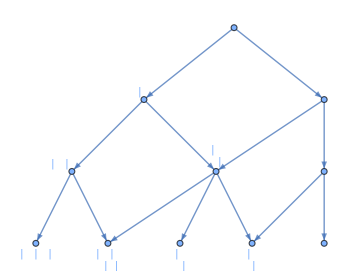

Figure 1. The Bratteli diagram for the canonical tower of subgroups for the symmetric group 𝒮_4.

The edges out of a node λ_(k-1) of 𝒢_(k-1) represent a complete set of orthogonal embeddings of the corresponding representation space into the representations λ_k of 𝒢_k. Conversely, the edges into a given representation λ_k of 𝒢_k index a set of mutually orthogonal subspaces of 𝒱_λ_k whose direct sum represents the decomposition of 𝒱_λ_k under the restriction of λ_k to 𝒢_(k-1).

More generally, the paths from the root node to a node λ of 𝒢 index a basis of 𝒱_λ with following property: For any 𝒢_k⊂𝒢, there is a partition of basis vectors of into subsets such that each subset spans an irreducible 𝒢_k-invariant subspace. Under this partition, the associated matrix representation restricted to 𝒢_k is block-diagonal, and the blocks corresponding to equivalent irreducible representations are identical. Such basis is called a subgroup-adapted basis or Gelfand-Tsetlin basis.

Definition

Let {g|g∈𝒢} is the right regular basis of group 𝒢, i.e.,  the canonical basis of the vector space that carries the right regular representation R of 𝒢. For all elements g and h of 𝒢,
	R̂(g)h=h g^-1 .

The right Fourier basis of the right regular representation consists of vectors ρ,ij defined by
	ρ,ij=Σ_(g∈𝒢)g √(d_λ/(|𝒢|))ρ_ij(g)
for each irreducible representation  ρ of 𝒢 and each index i,j=1,2,…,d_ρ. The basis change from the canonical to Fourier basis is called the quantum Fourier transform over group 𝒢 or simply the generalized quantum Fourier transform. The inverse transform gives
	g=Σ_(ρ∈[𝒢])Σ_(i,j∈[ρ])ρ,ij √(d_ρ/(|𝒢|))ρ_ij^*(g) ,
where [𝒢] denotes the set of all inequivalent irreducible representations of 𝒢 whereas [ρ] is the index set for the basis of ρ. Note that the dimension of an irreducible representation ρ of a finite group 𝒢 always divides the order of 𝒢, i.e., |𝒢|/d_ρ∈ℤ.

Under the group action, the Fourier basis transforms as
	R̂(g)ρ,ij=Σ_(k∈[ρ])ρ,ikρ_kj(g)
with index i belongs to the multiplicity space. Note that every basis vector ρ,ij transforms in the same way regardless of index i. That is to say, in the Fourier basis {ρ,ij}, the right regular representation R is block-diagonal in the form
	R(g)=⊕_ρ I_ρ⊗ρ,
where I_ρ refers to the d_ρ×d_ρ identity matrix in the multiplicity space.

### Conventions

Depending on which of the left and right regular representations is assumed and on whether the representation space is put on the left or right side of the multiplicity space, we have four conventions.

The Right-Right Convention (FourierParameterspaclet:ref/FourierParameters→{"Right", "Right"}):

ρ,ij:=Σ_(g∈𝒢)g √(d_ρ/(|𝒢|))ρ_ij(g)

g=Σ_(ρ∈[𝒢])Σ_(i,j∈[ρ])ρ,ijρ_ij^*(g)

R̂(g)ρ,ij:=Σ_(k∈[ρ])ρ,ikρ_kj(g)

R≐⊕_ρ I_d_ρ⊗ρ

The Left-Right Convention (FourierParameterspaclet:ref/FourierParameters→{"Left", "Right"}):

ρ,ij:=Σ_(g∈𝒢)g √(d_ρ/(|𝒢|))ρ_ij(g^-1)

g=Σ_(ρ∈[𝒢])Σ_(i,j∈[ρ])ρ,ijρ_ji(g)

L̂(g)ρ,ij:=Σ_k ρ,ikΓ_kj^ρ(g)

L≐⊕_ρ I_d_ρ⊗ρ

The Right-Left Convention (FourierParameterspaclet:ref/FourierParameters→{"Right", "Left"}):

ρ,ij:=Σ_(g∈𝒢)g √(d_ρ/(|𝒢|))ρ_ji(g)

g=Σ_(ρ∈[𝒢])Σ_(i,j∈[ρ])ρ,ijρ_ij(g^-1)

R̂(g)ρ,ij:=Σ_(k∈[ρ])ρ,kjρ_ki(g)

R≐⊕_ρ ρ⊗I_d_ρ

The Left-Left Convention (FourierParameterspaclet:ref/FourierParameters→{"Left", "Left"}):

ρ,ij:=Σ_(g∈𝒢)g √(d_ρ/(|𝒢|))ρ_ij^*(g)

g=Σ_(ρ∈[𝒢])Σ_(i,j∈[ρ])ρ,ijρ_ij(g)

L̂(g)ρ,ij:=Σ_(k∈[ρ])ρ,kjρ_ki(g)

L≐⊕_ρ ρ⊗I_d_ρ

### Example

Here, we demonstrate that in the Fourier basis, the regular representation is block diagonalized.

Consider the symmetric group S_n:

```mathematica
$n=3;
grp=SymmetricGroup[$n]
```

SymmetricGroup[3]

Consider the group generators:

```mathematica
gnr=GroupGenerators[SymmetricGroup@$n];
gnr//PermutationForm
```

{π_12,π_123}

Get the left regular representation of the group generators in the regular basis (i.e., computational basis):

```mathematica
rep=YoungRightRepresentation[$n]
```

YoungRightRepresentation[SymmetricGroup[3]]

```mathematica
mat=rep/@gnr
```

{SparseArray[…],SparseArray[…]}

```mathematica
MatrixForm/@mat
```

{(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0)}

To examine the regular representation in the Fourier basis, construct the matrix of basis change:

```mathematica
trs=YoungFourierMatrix[$n];
trs//MatrixForm
```

(1/(√6) | 1/(√3) | 0 | 0 | 1/(√3) | 1/(√6)
1/(√6) | -1/(2 √3) | 1/2 | 1/2 | 1/(2 √3) | -1/(√6)
1/(√6) | 1/(√3) | 0 | 0 | -1/(√3) | -1/(√6)
1/(√6) | -1/(2 √3) | 1/2 | -1/2 | -1/(2 √3) | 1/(√6)
1/(√6) | -1/(2 √3) | -1/2 | 1/2 | -1/(2 √3) | 1/(√6)
1/(√6) | -1/(2 √3) | -1/2 | -1/2 | 1/(2 √3) | -1/(√6))

```mathematica
Options[YoungFourierMatrix]
```

{FourierParameters→{Right,Right}}

Get the regular representation of the group generators in the Fourier basis:

```mathematica
Transpose[trs].mat[[1]].trs//Simplify//MatrixForm
Transpose[trs].mat[[2]].trs//Simplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1)

(1 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | (√3)/2 | 0 | 0 | 0
0 | -(√3)/2 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | (√3)/2 | 0
0 | 0 | 0 | -(√3)/2 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 1)

Quantum Implementation

We first find the relation between the computational and Fourier bases of the induced representation. Based on the relation, we then show how to implement the QFT efficiently on a quantum computer.

### Fourier Basis for Induced Representation

Let ℋ be a subgroup of a finite group 𝒢. Consider an irreducible representation Γ^μ of ℋ, and its induced representation Γ^μ↑_ℋ^𝒢 into 𝒢. Note that an induced representation can be defined for any representation of ℋ, but the representation must be irreducible in order to define the QFT for its induced representation. We choose an irreducible basis {μ,ij:j∈[d_μ]} for the representation space of Γ^μ by fixing an i∈[d_μ],
	(Γ̂)^μ(g)μ,ij=Σ_k μ,ikΓ_kj^μ(g).

The computational basis of the induced representation (Γ̂)^μ↑_ℋ^𝒢(g) is given by μ,ij⊗ℋt, where 𝒯:={t_i:i=1,2,…,|𝒢|/|ℋ|} is a fixed transversal for the right cosets of ℋ in 𝒢 and  {ℋt:t∈𝒯} is the canonical basis of the coset module (see above).

The QFT for the induced representation gives a basis {μ;λ,pq} in which the above representation is block diagonal. Here, λ labels the irreducible representations of 𝒢, p the multiplicity space and q the irreducible space.

The QFT is given by

μ;λ,pq=Σ_(t∈𝒯)Σ_(j∈[d_μ])μ,ij⊗ℋt √(d_λ/(|𝒢|))√(d_μ/(|ℋ|))(Σ_(h∈ℋ)[Γ_ij^μ(h)])^*Γ_pq^λ(ht) .

for a fixed i∈[d_μ] referring to a multiplicity space of irreducible representation μ of ℋ.  One can show that this basis indeed block-diagonalizes the induced representation,
	(Γ̂)^μ↑_ℋ^𝒢(g)μ;λ,pq=∑_(r∈[d_λ]) μ;λ,prΓ_rq^λ(g).

The inverse QFT is given by

μ,ij⊗ℋt=Σ_(λ∈𝒞_μ)Σ_(p,q∈[d_λ])μ;λ,pq √((d_μ d_λ)/(|ℋ||𝒢|))Σ_(h∈ℋ)(Γ_ij^μ(h) [Γ_pq^λ(ht)])^* ,

where i is a fixed parameter referring to a multiplicity space of irreducible representation μ of ℋ and 𝒞_μ is the set of children of μ in the Bratteli diagram.

On quantum computers, the above QFT can be achieved by the QFT over ℋ and then the inverse QFT over 𝒢 (both using the right-right convention).

### Recursive Implementation

Now, to implement the generalized QFT, let us rewrite v_i as μ,ij for a fixed j and the above equation as

t⊗μ,ij=Σ_(λ∈ℛ(𝒢))Σ_(p,q∈λ)λ,pq √((d_μ d_λ)/(|ℋ||𝒢|))Σ_(h∈ℋ)(Γ_pq^λ(th)[Γ_ij^μ(h)])^* .

Using the great orthogonality theorem, one can rewrite the above equation as

t⊗μ,ij=Σ_(λ∈𝒞_μ)((Γ̂)^λ(t)⊗Î)(λ,i_λ⊗λ,j_λ)=Σ_(λ∈𝒞_μ)Σ_k λ,k;μ,jΓ_(k i_λ)^λ(t_i) ,

where i_λ (and similarly j_λ) is the unique path in the Bratteli diagram such that i_λ|_(n-1)=i and 𝒞_μ is the set of children of μ in the Bratteli diagram. This relation induces a basis change from t⊗μ,ij to λ,p;μ,q, the Young interim basis (or modified Young-Fourier basis). Another basis change from λ,p;μ,q to λ,ij is a simple rearrangement. Finally, the inverse transformation of the above is given by

λ,p;μ,q=Σ_(t∈𝒯)Σ_k t⊗μ,kqΓ_(k_λ p)^λ(t)=Σ_(t∈𝒯)t⊗(L̂(t)λ,p q_λ) .

On a quantum computer, this may be regarded as the controlled-L̂ transformation on the embedded basis λ,p q_λ. Recall that the left regular representation is a native operator on the group algebra residing on the quantum register of the quantum computer.

Basic Application for Restricted Representations

Consider a subgroup ℋ of a finite group 𝒢. Let Γ^λ be an irreducible representation of 𝒢 with basis 
	{λ,i:i=1,…,d_λ}.
We want to find a ℋ-adapted basis
	{λ↓μ,kl:μ∈ℛ(ℋ), μ∈𝒞_λ; k∈[μ];l=1,…,m_μλ} ,
where λ↓μ indicates the restriction of λ,
	𝒞_λ:={μ∈ℛ(ℋ):μ->λ}
with μ→λ indicating that μ is a parent of λ in the Bratteli diagram, and m_μλ is the multiplicity of Γ^μ in Γ^λ↓_ℋ^𝒢. This basis transforms as
	Γ^λ↓_ℋ^𝒢(h)μ,ql=Σ_(p=1)^d_μ μ,plΓ_pq^μ(h)
for all h∈ℋ; that is, Γ^λ↓_ℋ^𝒢 is block-diagonal in this basis. Such a basis is called the subgroup-adapted basis.

The computational (or canonical) basis of the restricted representation Γ^λ↓_ℋ^𝒢 is 
	{h:h∈ℋ}. 
To use the quantum Fourier transform, we regard λ,i  as λ,ij  for fixed j∈λ, and extend the computational basis of Γ^λ↓_ℋ^𝒢 to
	{h⊗t:h∈ℋ; t∈𝒯 },
where 𝒯 is a transversal for the left cosets of ℋ in 𝒢. The required ℋ-adapted basis has the form
	{μ,kl⊗t:μ∈ℛ(H); k,l∈μ; t∈𝒯 }.
Here, l∈μ and t∈𝒯 together refer to the basis vectors of the m_μλ-dimensional multiplicity space of Γ^μ in Γ^λ↓_ℋ^𝒢. Note that transversal elements are required because it may happen that m_μλ>d_μ, and in such a case, l alone cannot refer to all basis vectors of the multiplicity space. One drawback of this approach is that all pairs (l,t) may not be linearly independent; the resulting basis may have some redundancy.

Now, performing the inverse quantum Fourier transform over ℋ and successively quantum Fourier transform over 𝒢 leads to
	μ,kl⊗t=Σ_(i,j∈λ)λ,ij √(d_λ/(|𝒢|))√(d_μ/(|ℋ|))(Σ_(h∈ℋ)[Γ_kl^μ(h)])^*Γ_ij^λ(ht)
for fixed j∈λ. One can show that for fixed l, this Fourier basis transforms as
	Γ^λ↓_ℋ^𝒢(h)μ,ql⊗t=Σ_(p∈μ)μ,pl⊗tΓ_pq^μ(h) ,
and hence it block-diagonalizes Γ^λ↓_ℋ^𝒢 in ℋ⊂𝒢, meaning that the basis is indeed a subgroup-adapted basis, and the associated representation is called a ℋ-adapted representation of 𝒢.

Basic Application for Induced Representations

This has already been seen in the quantum implementation of the generalized QFT. In fact, the implementation uses the QFT for the induced representation.

Generalized Quantum Phase Estimation

The generalized quantum phase estimation is an algorithm to find an irreducible representation in a reducible representation. It uses the generalized quantum Fourier transform.

(to be completed later)

Appendix

### Transversal for Cosets of S_(n-1) in S_n

𝒯:={π_(12…n)^k:k=0,1,2,…,n-1} is a transversal for the cosets of S_(n-1) in S_n as illustrated below. This transversal is useful to construct a subgroup adapted basis associated with the canonical tower of subgroups of the symmetric group.

Set the degree of the symmetric group:

```mathematica
$n=4;
```

Get the elements of the symmetric group S_n:

```mathematica
elm=YoungElements[$n];
elm//PermutationForm
```

{π_0,π_34,π_23,π_234,π_243,π_24,π_12,π_12π_34,π_123,π_1234,π_1243,π_124,π_132,π_1342,π_13,π_134,π_13π_24,π_1324,π_1432,π_142,π_143,π_14,π_1423,π_14π_23}

Get the elements of the subgroup S_(n-1):

```mathematica
sub=YoungElements[$n-1];
sub//PermutationForm
```

{π_0,π_23,π_12,π_123,π_132,π_13}

Pick the transversal:

```mathematica
trs=Table[PermutationPower[Cycles@{Range@$n},k],{k,0,$n-1}];
trs//PermutationForm
```

{π_0,π_1234,π_13π_24,π_1432}

To verify that it is indeed a transversal, get the left and right cosets from the transversal:

```mathematica
left=Sort/@Outer[PermutationProduct[#2,#1]&,trs,sub];
Thread[trs->left]//PermutationForm//TableForm
```

π_0→{π_0,π_12,π_13,π_23,π_123,π_132}
π_1234→{π_14,π_124,π_134,π_1234,π_1324,π_14π_23}
π_13π_24→{π_24,π_142,π_234,π_1342,π_1423,π_13π_24}
π_1432→{π_34,π_143,π_243,π_1243,π_1432,π_12π_34}

```mathematica
right=Sort/@Outer[PermutationProduct,InversePermutation/@trs,sub];
Thread[trs->right]//PermutationForm//TableForm
```

π_0→{π_0,π_12,π_13,π_23,π_123,π_132}
π_1234→{π_14,π_142,π_143,π_1423,π_1432,π_14π_23}
π_13π_24→{π_24,π_124,π_243,π_1243,π_1324,π_13π_24}
π_1432→{π_34,π_134,π_234,π_1234,π_1342,π_12π_34}

| Related Guides
▪Quantum Information Systems
▪Q3: Symbolic Quantum Simulation

| Related Tech Notes
▪Dual Quantum Schur Transform
▪Quantum Fourier Transform
▪Quantum Phase Estimation
▪Quantum Algorithms
▪Quantum Information Systems with Q3
▪Quick Quantum Computing with Q3

| Related Links
▪R. Beals (1997)https://doi.org/10.1145/258533.258548, “Quantum computation of Fourier transforms over symmetric groups” in Proceedings of the twenty-ninth annual {ACM} symposium on Theory of computing  (1997).
▪C. Moore, D. Rockmore and A. Russell (2004)https://dl.acm.org/doi/10.5555/982792.982910, “Generic quantum Fourier transforms” in Proceedings of the fifteenth annual ACM-SIAM symposium on Discrete algorithms (SODA) (January, 2004).
▪B. E. Sagan (2001)https://doi.org/10.1007/978-1-4757-6804-6, The Symmetric Group, 2nd ed. (Springer, 2001).